### In this notebook we will use the Euler Lagrange approach to solving an ODE. This illustrates the power of Mathematica, where symbolic calculations are easily performed. Let’s start by defining our Lagrangian.

```mathematica
Kinetic = 1/2 m (x'[t])^2;
Potential = 1/2 k(x[t])^2;
Lagrangian = Kinetic - Potential
```

-1/2 k x[t]^2+1/2 m x'[t]^2

### We apply the Euler Lagrange equations to find the correct ODE

```mathematica
ODE = D[D[Lagrangian, x'[t]],t]-D[Lagrangian,x[t]]==0
```

k x[t]+m x''[t]==0

### The solutions can now be found with DSolve (Differential Solve)

```mathematica
Sols=DSolve[{ODE, x[0]==10,x'[0]==0},x[t],t][[1]]
```

{x[t]→10 Cos[(√k t)/(√m)]}

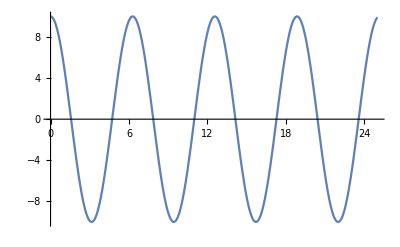

```mathematica
Plot[x[t]/.Sols/.{k->1,m->1},{t,0,25}]
```

### Now we repeat this process, but for a full forced damped oscillator. We skip using Euler-Lagrange. Some research will reveal that it can be done, however the non-conservative force gives an explicitly time dependent Lagrangian.

```mathematica
ODE = m x''[t]+b x'[t]+k x[t] == F0 Cos[ω t];
Sols=DSolve[{ODE, x[0]==0,x'[0]==0},x[t],t][[1]];
```

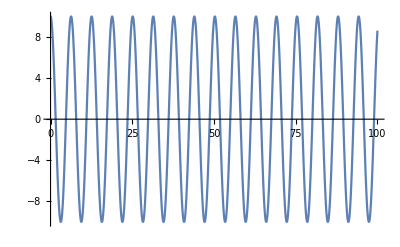

```mathematica
Plot[x[t]/.Sols/.{k->1,m->1,b->0.1,F0->10,ω->2},{t,0,100}]
```

### For cases with no analytic solution we can use a numerical solution NDSolve

```mathematica
(*Code 'borrowed' and slightly adapted from Wikipedia*)
tend=50;
eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]};
init={x[0]==10,y[0]==10,z[0]==10};
pars={σ->10,ρ->28,β->8/3};
Sols=NDSolve[{eq/. pars,init},{x,y,z},{t,0,tend}][[1]];
ParametricPlot3D[{x[t],y[t],z[t]}/.Sols,{t,0,tend}]
```

-Graphics3D-